```mathematica
Assuming[{0<a<1,0<θ<π/2},∫1/(Cos[θ]+a*(Cos[θ])^2)ⅆθ]
```

-(2 a ArcTanh[((-1+a) Tan[θ/2])/(√(-1+a^2))])/(√(-1+a^2))-Log[Cos[θ/2]-Sin[θ/2]]+Log[Cos[θ/2]+Sin[θ/2]]

```mathematica
Assuming[a>0,Integrate[1/(Sqrt[u^2 + 1] + a), u]]
```

ArcSinh[u]+(a (-ArcTan[u/(√(1-a^2))]+ArcTan[(a u)/(√(1-a^2) √(1+u^2))]))/(√(1-a^2))

```mathematica
μ[r_,rs_,c_] := (1/(Log[1+c]-(c/(1+c))))*(Log[1+(r/rs)]-((r/rs)/(1+r/rs)) )
```

```mathematica
Assuming[{rs>p>0, c>0},Series[μ[p,rs,c],{p,0,2}]]
```

p^2/(2 rs^2 (-c/(1+c)+Log[1+c]))+O[p]^3

```mathematica
Plot[-(2 a ArcTanh[((-1+a) Tan[π/2])/(√(-1+a^2))])/(√(-1+a^2)),{a,0.1,0.9}]
```

-Graphics-

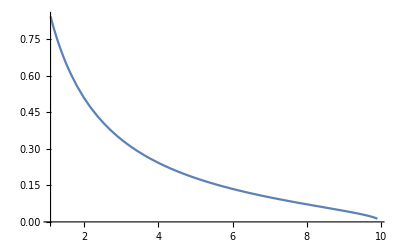

```mathematica
Plot[ 1/(√(-p^2+1^2))*Log[arg[p,1,10]],{p,1.1,9.9}]
```

```mathematica
Assuming[{p>rs,c>1},ComplexExpand[ Log[arg[p,rs,c]]]]
```

ⅈ Arg[(1+√((-p+rs)/(p+rs)) √((-p+c rs)/(p+c rs)))/(1-√((-p+rs)/(p+rs)) √((-p+c rs)/(p+c rs)))]+Log[(√((((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+c rs)/(p+c rs)]] Sin[1/2 Arg[(-p+rs)/(p+rs)]]+((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+rs)/(p+rs)]] Sin[1/2 Arg[(-p+c rs)/(p+c rs)]])^2+(1+((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+rs)/(p+rs)]] Cos[1/2 Arg[(-p+c rs)/(p+c rs)]]-((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Sin[1/2 Arg[(-p+rs)/(p+rs)]] Sin[1/2 Arg[(-p+c rs)/(p+c rs)]])^2))/(√((-((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+c rs)/(p+c rs)]] Sin[1/2 Arg[(-p+rs)/(p+rs)]]-((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+rs)/(p+rs)]] Sin[1/2 Arg[(-p+c rs)/(p+c rs)]])^2+(1-((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Cos[1/2 Arg[(-p+rs)/(p+rs)]] Cos[1/2 Arg[(-p+c rs)/(p+c rs)]]+((-p+rs)^2/(p+rs)^2)^(1/4) ((-p+c rs)^2/(p+c rs)^2)^(1/4) Sin[1/2 Arg[(-p+rs)/(p+rs)]] Sin[1/2 Arg[(-p+c rs)/(p+c rs)]])^2))]

```mathematica
Assuming[{p>rs,c>1},FullSimplify[Log[arg[p,rs,c]]]]
```

Log[-(1+√(1-(2 p)/(p+rs)) √(1-(2 p)/(p+c rs)))/(-1+√(1-(2 p)/(p+rs)) √(1-(2 p)/(p+c rs)))]